Определим множество ребер :

```mathematica
Ed={{1,2,1},{1,3,7},{1,4,8},{1,6,3},{2,5,3},{2,7,9},{3,4,8},{4,9,8},{5,8,6},{6,11,9},{7,3,2},{7,6,9},{7,8,1},{8,9,7},{8,13,5},{9,11,10},{9,13,7},{9,14,1},{11,13,9},{11,14,3},{13,16,4},{13,17,5},{14,18,7},{14,19,9},{16,17,10},{16,18,9},{17,20,2},{18,20,7},{19,5,7},{19,20,7}};
```

```mathematica
vertices=Union[Flatten[Ed[[All,{1,2}]]]];
edges=UndirectedEdge@@@Ed[[All,{1,2}]];
weights=Ed[[All,3]];
```

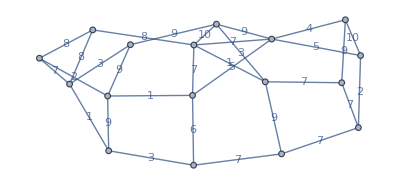

```mathematica
g=Graph[vertices,edges,EdgeWeight->weights,EdgeLabels->"EdgeWeight"]
```

Ребро e

```mathematica
e = UndirectedEdge[9,11]
```

9<->11

Для того, что бы минимальное остовное дерево содержало конкретное ребро, сопоставим ему нулевой вес

```mathematica
(*Устанавливаем вес ребра e в 0*)
adjustedWeights=ReplacePart[PropertyValue[{g,EdgeWeight}],Position[EdgeList[g],e]->0];

(*Обновляем граф с новыми весами*)
adjustedGraph=SetProperty[g,EdgeWeight->adjustedWeights];

(*Находим минимальный остов*)
spanningTree=FindSpanningTree[adjustedGraph,EdgeWeight->adjustedWeights];

(*Отображение результата*)
HighlightGraph[g,spanningTree]
```

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

FindSpanningTree::graph: A graph object is expected at position 1 in ….

-Graphics-